## Minimization test

```mathematica
ClearAll["Global*`"]
```

### Constants

```mathematica
a=3.4;
b=1-a;
th=0.2;
phi=1.2;
c0=2.4;
```

### Model function

```mathematica
f[x_,y_]:=a*(x^2 Sin[th]-c0)+b(y^2 Cos[th]Sin[phi]-c0)-x y;
```

```mathematica
contour[function_]:=ContourPlot[function[x,y],{x,-1,1},{y,-1,1},FrameLabel->{"x","y"},Frame->True,Axes->False];
```

### Create exporter

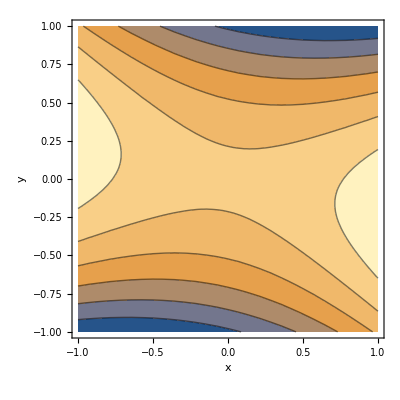

```mathematica
export[path_,object_]:=Export[StringTemplate["````.pdf"][NotebookDirectory[],path],object,ImageResolution->1200];
export["contour",contour[f]];
Show[contour[f]]
```

```mathematica
minPoint=NMinimize[{f[x,y],-1≤x≤1,-1≤y≤1},{x,y}];
maxPoint=NMaximize[{f[x,y],-1≤x≤1,-1≤y≤1},{x,y}];
```

```mathematica
Print[minPoint,"\n",maxPoint]
```

{-4.96241,{x→0.740224,y→1.}}
{-1.61049,{x→1.,y→-0.228071}}